# Kitaev Honeycomb lattice with B field

let  n  be the number of hexagons in the vertical direction. The horizontal direction is assumed to have translational symmetry. Assume that we already take the Fourier transform, and thus the lattice collapse to a kind of SSH chain.

We have first NN of strength:  J
And second NNN of strength:  κ

```mathematica
ClearAll[J,k,κ,h,n]
```

## The Hamiltonian ( and others definitions )

Lets define the interaction term that appear in the Bloch Hamiltonian.

```mathematica
r[J_]=2J;
s[k_,J_]=-4J Cos[k/2];
α[k_,κ_] = 4 κ Sin [k];
β[k_,κ_] =  4 κ Sin [k/2];
γ[h_] = -2h;
```

where:

	n  gives the dimension:  2n+2  c  fermions  and 2  b fermions ;
	J is the Kitaev interaction (homogeneous and isotropic ; 
	κ is the strength of the magnetic term that breaks the time-reversal symmetry ;
	

	The Hamiltonian in k-space :
		• The ordering of the vectors in the space is:
		• ( b_1 c_2 ... c_(L-1) b_L )^T

```mathematica
H[k_,n_, J_,κ_,h_] := SparseArray[   {
					{i_,i_} -> If[ 1<i<2n+ 4 , If[OddQ[i],-α[k,κ], α[k,κ]] , 0],

					{i_,j_} /;Abs[i-j]==1->   
												If[                     ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 
															If[ ((i==1)∨(i==2n+4)), ⅈ γ[h] , - ⅈ γ[h] ], 
															If[EvenQ[Min[i,j]], -(i-j) ⅈ s[k,J] , -(i-j) ⅈ r[J]] ],

					{i_,j_} /;Abs[i-j]==2-> If[ ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 0,  If[OddQ[i],β[k,κ], -β[k,κ]] ]
},					
	{2n+ 4,2n+ 4}					]
```

## Spectrum comparison

Let P denote the number of partitions (numerical discretization) in momentum space:

Lets define a function for the spectrum

```mathematica
Energies[n_,J_,κ_ ,h_, P_] :=  Table[  N@ {   k, Chop@Sort[Eigenvalues[ N@ H[k, n, J,κ,h] ]]    }     , {k,0,2π , 2π/P}]
```

the output of this function is of the form:

{ 
{ k_1 , { ϵ_1(k_1) , ϵ_2(k_1) , ... , ϵ_n(k_1) , ... }},
 {k_2  , { ϵ_1(k_2) , ϵ_2(k_2) , ... , ϵ_n(k_2) , ... }  },
 {... , {... } }  } 

We'll also use the following parameters :

```mathematica
n= 100;
P=100;
J=1;
```

The form in which we allocate the spectrum  is not suitable to plot  in energy versus momentum,  we need first reallocate to the form  { ... ,  { k , ϵ ( k ) } , ...}

```mathematica
dispersion[E_,P_,n_]:= Transpose[    Table[  { E⟦i⟧⟦1⟧ , E⟦i⟧⟦2⟧⟦j⟧} , {i,1,P} , {j,1,2*n+4}]  ]
```

### 1st : Zero Field and Zero kappa

Calculate all energies in the scenario  h = 0 and κ = 0,

 we will assign to the variable E00 and return the time necessary to perform the calculation in minutes:

```mathematica
Timing[E1 = Energies[n,1,0 ,0, P]]⟦1⟧ //Quiet
```

0.214792

```mathematica
D1 = dispersion[E1,P,n];
```

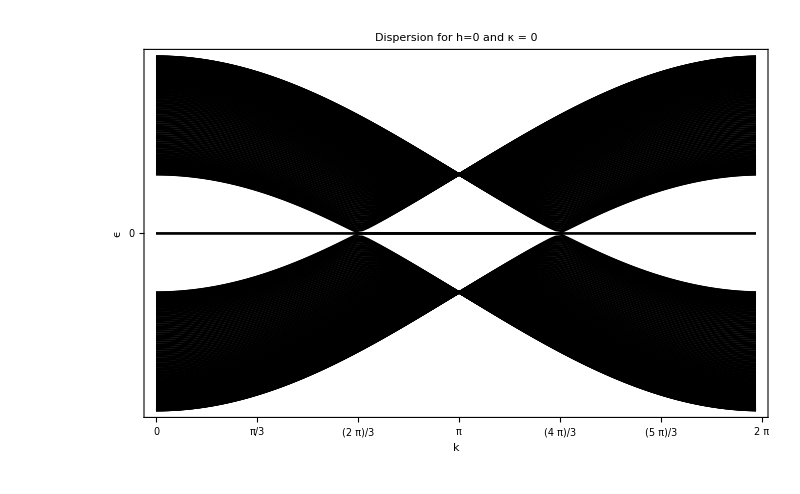

```mathematica
ListPlot[ D1 , FrameLabel->{k , ϵ }  ,  PlotLabel-> "Dispersion for h=0 and κ = 0"  ,   Ticks->Automatic , FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , {-2π,0,2π}}   ,Joined->True,PlotStyle->{Black},Frame->{{True,False} ,{True,False}}   ,FrameStyle->Directive[Black,16],ImageSize->800]
```

### 2nd : Zero Field and non-Zero kappa

h = 0  ,  κ = 0.1   ,  J = 1

```mathematica
Timing[E2 = Energies[n,1,0.1,0, P]]⟦1⟧ //Quiet
```

5.50981

```mathematica
D2 = dispersion[E2,P,n];
```

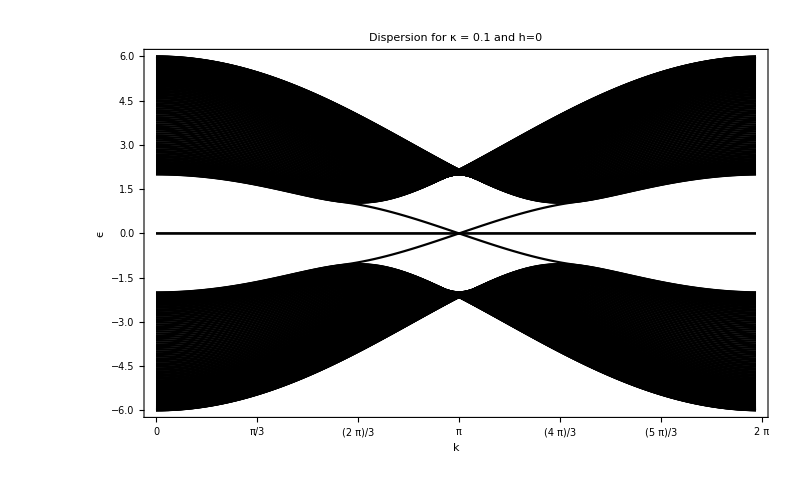

```mathematica
ListPlot[ D2 , FrameLabel->{k , ϵ }  ,  PlotLabel-> Style["Dispersion for κ = 0.1 and h=0",20 ,Black ] ,   FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800]
```

Zoom at low energies  and compute fermi velocity

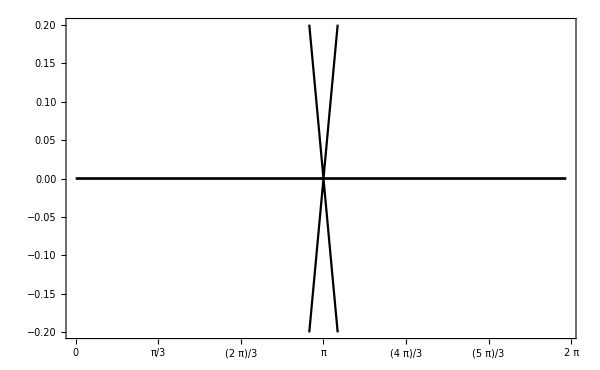

```mathematica
g1=ListPlot[D2,   FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->600,PlotRange->{-.2,.2}]
```

The  ⟦P/2+1⟧ factor of the energy  is gives  a section of the dispersion π  versus E(π) for all eigenvectors;   ⟦ P/2+1 + δ⟧ gives the section at π+δk  (of course δ should be a small and >1)
the ⟦2⟧ gives all eigenvalues (sorted) at k=π.
the ⟦n+4⟧ gives right at the middle of the spectrum ( as well as [n+1]  - note that [n+2] and [n+3] are both zero energy modes for this case )

```mathematica
δ = 10;
δk=(2π/P)δ;
vF = (E2⟦P/2+1+δ⟧⟦2⟧⟦n+1⟧-E2⟦P/2+1⟧⟦2⟧⟦n+1⟧)/δk
```

-1.04923

```mathematica
g2=Plot[vF (k-π),{k,π-1,π+1},PlotStyle->{Red,Dotted, Thin},Frame->True,FrameStyle->Directive[Black,16],ImageSize->500,PlotRange->All];
```

```mathematica
g3=Plot[-vF (k-π),{k,π-1,π+1},PlotStyle->{Blue,Dotted , Thin},Frame->True,FrameStyle->Directive[Black,16],ImageSize->500,PlotRange->All];
```

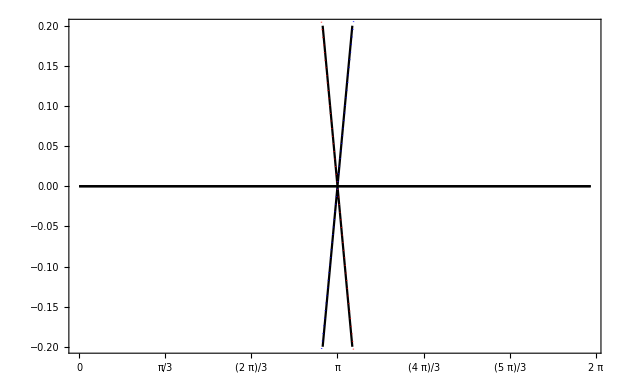

```mathematica
Show[g1,g2,g3]
```

### 3rd : non-Zero Field and Zero kappa

h = 1 = J ,  κ = 0

```mathematica
Timing[E3 = Energies[n,1,0,0.5, P]]⟦1⟧/60 //Quiet
```

0.0890593

```mathematica
D3 = dispersion[E3,P,n];
```

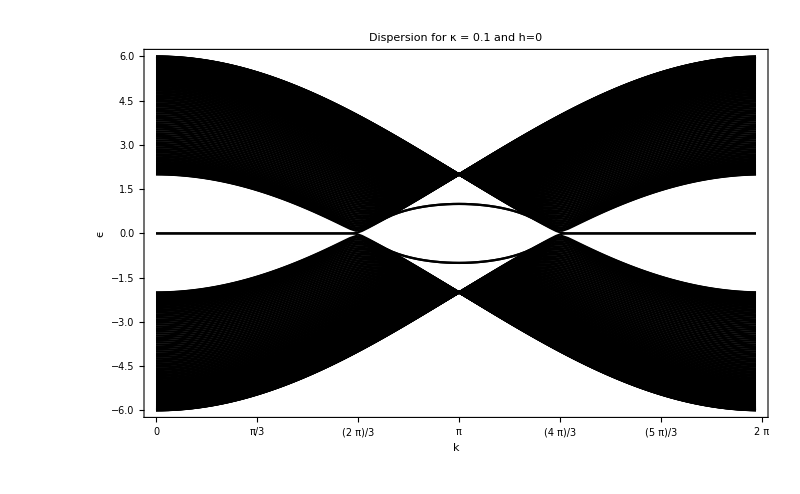

```mathematica
ListPlot[ D3 , FrameLabel->{k , ϵ }  ,  PlotLabel-> Style["Dispersion for κ = 0.1 and h=0",20 ,Black ] ,   FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800]
```

### 4th : non-Zero Field and non-Zero kappa

h  =  0.5,    κ  =  0.1  ,    J=1

```mathematica
Timing[E4 = Energies[n,1,0.1,0.5, P]]⟦1⟧//Quiet
```

5.74306

```mathematica
D4 =dispersion[E4,P,n];
```

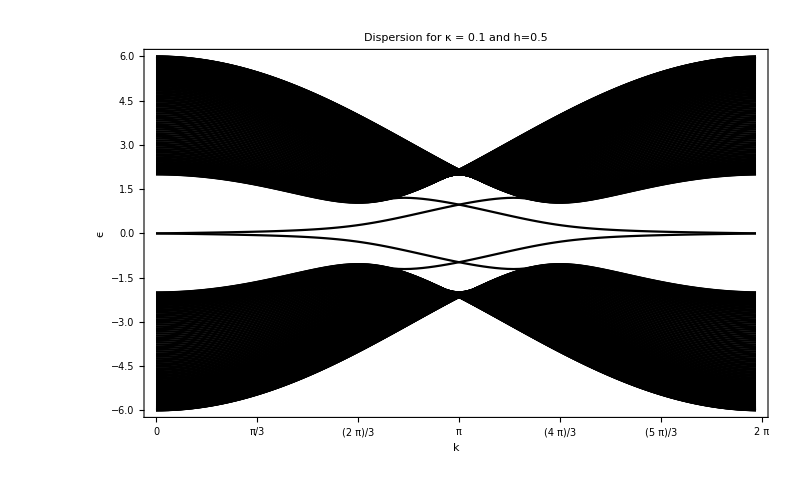

```mathematica
ListPlot[ D4 , FrameLabel->{k , ϵ }  ,  PlotLabel-> Style["Dispersion for κ = 0.1 and h=0.5",20 ,Black ] ,   FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800]
```

Zoom at low energies  and compute fermi velocity

```mathematica
g1=ListPlot[D4,   FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->600,PlotRange->{-.15,.15}];
```

The  ⟦P/2+1⟧ factor of the energy  is gives  a section of the dispersion π  versus E(π) for all eigenvectors;   ⟦ P/2+1 + δ⟧ gives the section at π+δk  (of course δ should be a small and >1)
the ⟦2⟧ gives all eigenvalues (sorted) at k=π.
the ⟦n+4⟧ gives right at the middle of the spectrum ( as well as [n+1]  - note that [n+2] and [n+3] are both zero energy modes for this case )

```mathematica
δ = 2;
δk=(2π/P)δ;
vF = (E4⟦1+δ⟧⟦2⟧⟦n+1⟧-E4⟦1⟧⟦2⟧⟦n+1⟧)/δk
```

0.0427033

```mathematica
g2=Plot[ k vF , {k,0,2}  , PlotLabels->Placed["             vF   =          "+vF, Top] ,PlotStyle->{Red,Dotted, Thin},Frame->True,FrameStyle->Directive[Black,16],ImageSize->500,PlotRange->All];
```

```mathematica
g3=Plot[ - k vF,{k,0,2}  ,PlotLabels->
Placed[ "             vF   =          "-vF , Bottom] , PlotStyle->{Blue,Dotted, Thin},Frame->True,FrameStyle->Directive[Black,16],ImageSize->500,PlotRange->All];
```

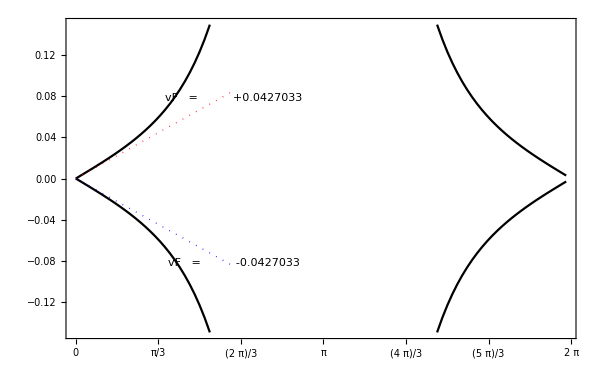

```mathematica
Show[g1,g2,g3]
```

### Iterative visualization

we will diminish the partition and the dimension of the system to allow a fast visualization of how the whole  [c.f. in the next section we will focus at the low-energy modes] dispersion changes with  κ  and  h

```mathematica
Manipulate[ ListPlot[  dispersion[Energies[n,1,κ ,h, 100], 100,n  ]    , FrameLabel->{k , ϵ }  ,   Ticks->Automatic , Joined->True, FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π} , {-6 ,-4,-2,0 , 2, 4 , 6}}   , Frame -> {{True,False},{True,False} }  ]
	 , {h,{ 0,0.5,1,2,5}}
	 , {κ,{0,0.5,1,2,5} }
	 ,{n,{15,50}}
		]
```

## Bulk and Edge spectrum

For the purpose of analyzing the edge modes I will look with caution only at the four modes nearest to the zero energy  [  read the  (L/2-1), (L/2),(L/2+1) and (L/2+2) -th  ]

The Edge  function in designed to give low-energy curves that do not belongs to the continuum spectrum. So we need four curves that are originated from the two b  and two c  Majorana fermion modes at the edge.
  
 Since we have L fermions in the system, and the spectrum is particle-hole symmetric, the low energy mode are around L/2. 
 
 The modes  L/2-1 , L/2 , L/2+1 and L/2+2      L = 2n+4

```mathematica
edge[D_,n_] := D⟦ {n+1,n+2,n+3,n+4} ⟧
```

The Bulk  function in designed to give the contour of the continuum spectrum. So we need four curves, two for positive energy, and two for negative.

```mathematica
Bulk[D_,n_] := D⟦ {1,n,n+5,2n+4} ⟧
```

Add we also define a function that generate a 8-tuple of dispersions. We’ll use it to draw a schematic graphic for the dispersion, since the bulk modes converges in to a band in the continuum limit, and then we need only the upper and lower curves that gives the shape for the band.

```mathematica
edgeBulk[D_,n_] := Join[ edge[ D ,n],Bulk[ D,n] ]
```

### 1st : Zero Field and Zero kappa

```mathematica
ed1 = edge[ D1,n];
```

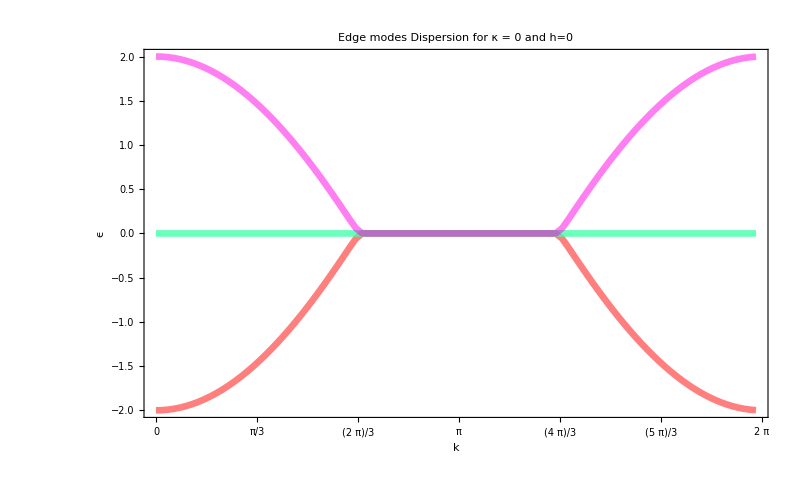

```mathematica
ListPlot[ ed1 , Joined->True ,  PlotRange->All, FrameLabel->{k , ϵ }  , FrameLabel->{k , ϵ }  ,  PlotLabel-> Style["Edge modes Dispersion for κ = 0 and h=0",20 ,Black ] ,
PlotStyle-> {              {Hue[0,1,1,.5] , Thickness[0.006]}  ,{Hue[0.22,1,1,.5], Thickness[0.006]}  ,
				   { Hue[0.5,1,1,.5] , Thickness[0.006] } , {Hue[0.85,1,1,.5] , Thickness[0.006] }
				},
   FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800]
```

```mathematica
bulk1 = Bulk[ D1,n];
```

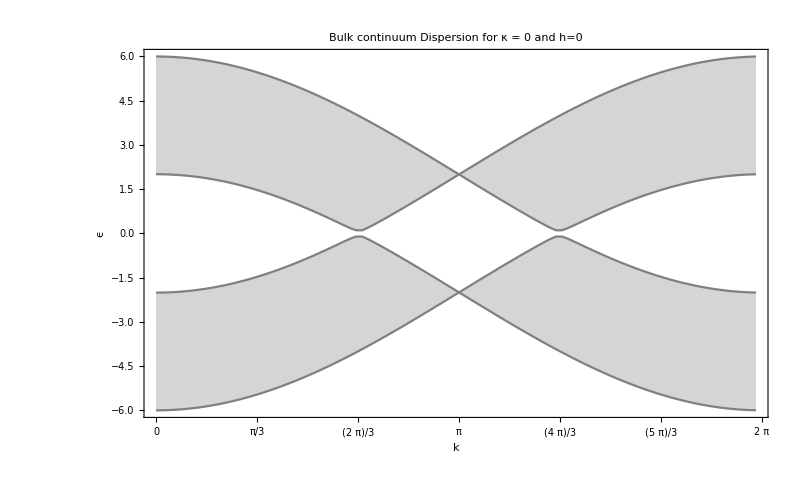

```mathematica
ListPlot[ bulk1 ,  Joined->True , FrameLabel->{k , ϵ }  , PlotLabel-> Style["Bulk continuum Dispersion for κ = 0 and h=0",20 ,Black ] ,  Filling->{2->{1}, 3-> {4}},FillingStyle->{GrayLevel[0.8,0.81]} ,PlotStyle->Gray , FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800 ]
```

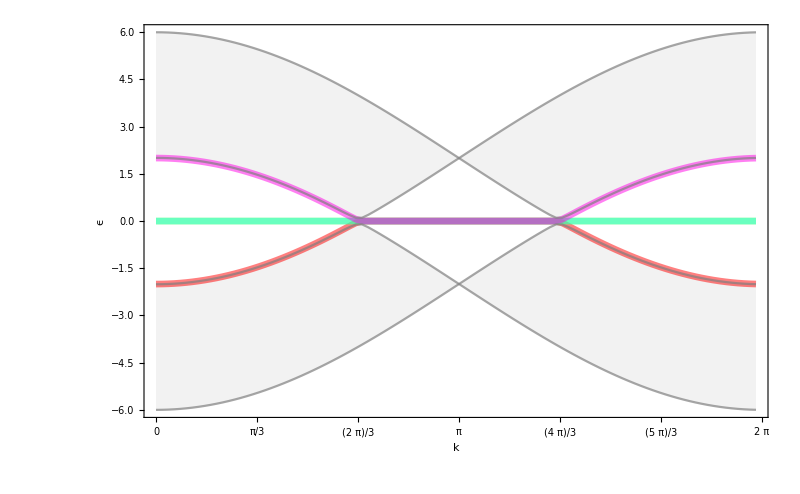

```mathematica
ListPlot[ edgeBulk[D1,n] 	
		,PlotStyle-> { {Hue[0,1,1,.5] , Thickness[0.006]} 
				,{Hue[0.22,1,1,.5], Thickness[0.006]}  , { Hue[0.5,1,1,.5] , Thickness[0.006] } , {Hue[0.85,1,1,.5] , Thickness[0.006] }
	                            ,Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7] ,Hue[1,0,0.5,0.7]}
		,FrameLabel->{k , ϵ }  
		, FillingStyle->Hue[0.5,0,.9,0.5] 
		, Filling->{6->{5}, 7-> {8}} ,
		 FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800  ]
```

### 2nd : Zero Field and non-Zero kappa

```mathematica
ed10 = edge[ D10,n];
```

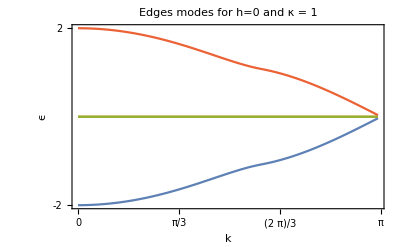

```mathematica
ListPlot[ ed10 ,  Joined->True , FrameLabel->{k , ϵ }  ,  PlotLabel-> "Edges modes for h=0 and κ = 1"  ,   Ticks->Automatic  , FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π}  , {-6,-4,-2,0,2,4,6}}   , Frame -> {{True,False},{True,False}} ]
```

```mathematica
bulk10 = Bulk[ D10,n];
```

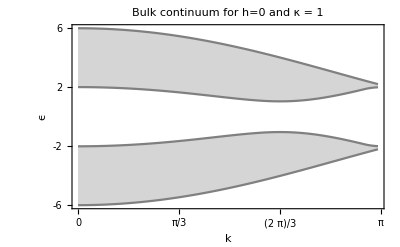

```mathematica
ListPlot[ bulk10 ,  Joined->True , FrameLabel->{k , ϵ }  ,  PlotLabel-> "Bulk continuum for h=0 and κ = 1"  ,  Ticks->Automatic  , FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π}  , {-6,-4,-2,0,2,4,6}}   , Frame -> {{True,False},{True,False}}  , Filling->{2->{1}, 3-> {4}},FillingStyle->{GrayLevel[0.8,0.81]} ,PlotStyle->Gray ]
```

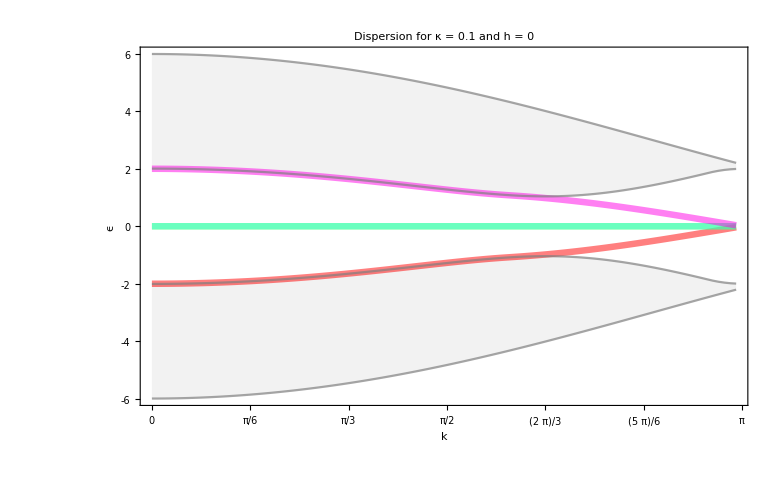

```mathematica
ListPlot[ 
		edgeBulk[D10,n] 	
		,  Joined->True 
		,PlotStyle-> { {Hue[0,1,1,.5] , Thickness[0.006]} 
				,{Hue[0.22,1,1,.5], Thickness[0.006]}  , { Hue[0.5,1,1,.5] , Thickness[0.006] } , {Hue[0.85,1,1,.5] , Thickness[0.006] }
	                            ,Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7] ,Hue[1,0,0.5,0.7]
				}
		,FrameLabel->{k , ϵ }  
		,  PlotLabel-> "Dispersion for κ = 0.1 and h = 0"  
		, FillingStyle->Hue[0.5,0,.9,0.5] 
		, Filling->{6->{5}, 7-> {8}} 
		,FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π} , {-6 ,-4,-2,0 , 2, 4 , 6}}   , Frame -> {{True,False},{True,False} }  ]
```

### 3rd : non-Zero Field and Zero kappa

h = 1 = J ,  κ = 0

```mathematica
ed01 = edge[ D01,n];
```

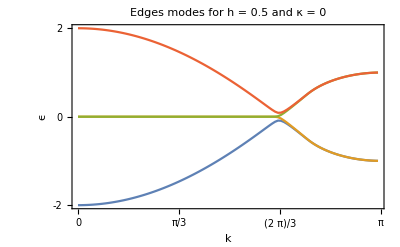

```mathematica
ListPlot[ ed01 ,  Joined->True , FrameLabel->{k , ϵ }  ,  PlotLabel-> "Edges modes for h = 0.5 and κ = 0"  ,  Ticks->Automatic  , FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π}  , {-6,-4,-2,-1 , 0,1, 2,4,6}}    , Frame -> {{True,False},{True,False}} ]
```

```mathematica
bulk01 = Bulk[ D01,n];
```

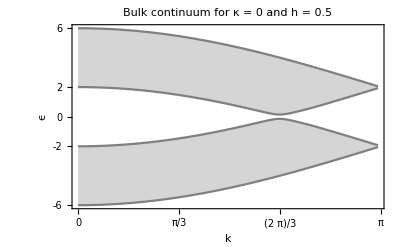

```mathematica
ListPlot[ bulk01 ,  Joined->True , FrameLabel->{k , ϵ }  ,  PlotLabel-> "Bulk continuum for κ = 0 and h = 0.5"  ,   Ticks->Automatic  , FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π}  , {-6,-4,-2,-1 , 0,1, 2,4,6}}    , Frame -> {{True,False},{True,False}}  , Filling->{2->{1}, 3-> {4}},FillingStyle->{GrayLevel[0.8,0.81]} ,PlotStyle->Gray ]
```

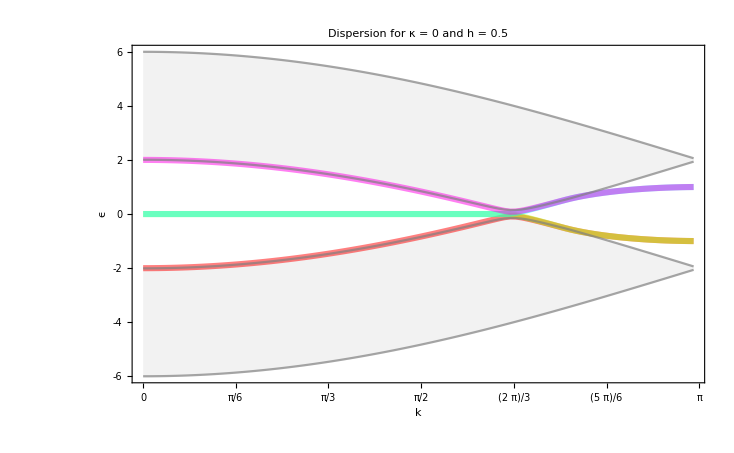

```mathematica
ListPlot[ 
		edgeBulk[D01,n] 	
		,  Joined->True 
		,PlotStyle-> { {Hue[0,1,1,.5] , Thickness[0.006]} 
				,{Hue[0.22,1,1,.5], Thickness[0.006]}  , { Hue[0.5,1,1,.5] , Thickness[0.006] } , {Hue[0.85,1,1,.5] , Thickness[0.006] }
	                            ,Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7] ,Hue[1,0,0.5,0.7]
				}
		,FrameLabel->{k , ϵ }  
		,  PlotLabel-> "Dispersion for κ = 0 and h = 0.5 "  
		, FillingStyle->Hue[0.5,0,.9,0.5] 
		, Filling->{6->{5}, 7-> {8}} 
		,FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π} , {-6 ,-4,-2,0 , 2, 4 , 6}}   , Frame -> {{True,False},{True,False} }  ]
```

### 4th : non-Zero Field and non-Zero kappa

h  = 0.5 ,  κ  =  0.3

```mathematica
ed11 = edge[ D11,n];
```

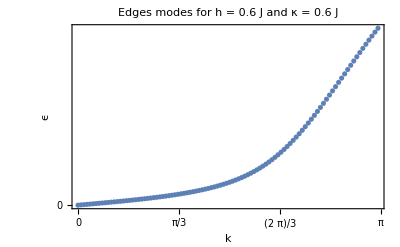

```mathematica
ListPlot[ ed11[[3]] ,  Joined->False, FrameLabel->{k , ϵ }  ,  PlotLabel-> "Edges modes for h = 0.6 J and κ = 0.6 J"  ,  Ticks->Automatic  , FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π}  , {-6,-4,-2,-1 , 0,1, 2,4,6}}    , Frame -> {{True,False},{True,False}} ]
```

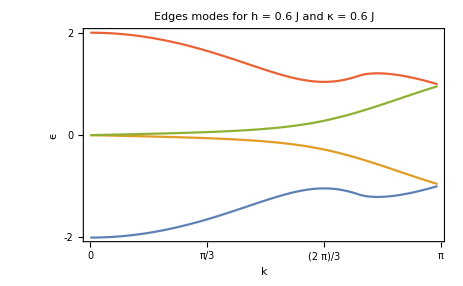

```mathematica
ListPlot[ ed11 ,  Joined->True , FrameLabel->{k , ϵ }  ,  PlotLabel-> "Edges modes for h = 0.6 J and κ = 0.6 J"  ,  Ticks->Automatic  , FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π}  , {-6,-4,-2,-1 , 0,1, 2,4,6}}    , Frame -> {{True,False},{True,False}} ]
```

```mathematica
bulk11 = Bulk[ D11,n];
```

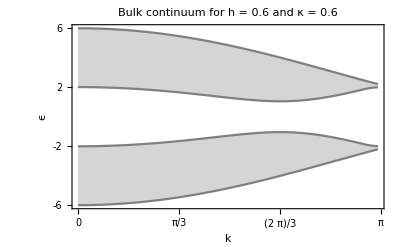

```mathematica
ListPlot[ bulk11 ,  Joined->True , FrameLabel->{k , ϵ }  ,  PlotLabel-> "Bulk continuum for h = 0.6 and κ = 0.6"  ,   Ticks->Automatic  , FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π}  , {-6,-4,-2 , 0, 2,4,6}}  , Frame -> {{True,False},{True,False}} , Filling->{2->{1}, 3-> {4}},FillingStyle->{GrayLevel[0.8,0.81]} ,PlotStyle->Gray ]
```

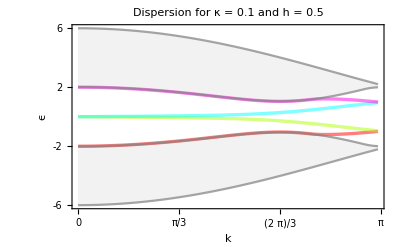

```mathematica
ListPlot[ 
		edgeBulk[D11,n] 	
		,  Joined->True 
		,PlotStyle-> { {Hue[0,1,1,.5] , Thickness[0.006]} 
				,{Hue[0.22,1,1,.5], Thickness[0.006]}  , { Hue[0.5,1,1,.5] , Thickness[0.006] } , {Hue[0.85,1,1,.5] , Thickness[0.006] }
	                            ,Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7] ,Hue[1,0,0.5,0.7]
				}
		,FrameLabel->{k , ϵ }  
		,  PlotLabel-> "Dispersion for κ = 0.1 and h = 0.5"  
		, FillingStyle->Hue[0.5,0,.9,0.5] 
		, Filling->{6->{5}, 7-> {8}} 
		,FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π} , {-6 ,-4,-2,0 , 2, 4 , 6}}   , Frame -> {{True,False},{True,False} }  ]
```

### Iterative visualization

When we join the ed + bulk  we obtain 8 lines.

The first four are for the edge and I colored they.

The other four are for the bulk and I leave it gray.

```mathematica
Manipulate[
ListPlot[ 
		edgeBulk[ dispersion[Quiet@Energies[n,1,κ ,h, P], P,n ],n] 	
		,PlotStyle-> { {Black , Thickness[0.006]} 
				,{Black, Thickness[0.006]}  , { Black , Thickness[0.006] } , {Black , Thickness[0.006] }
	                            ,Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7] ,Hue[1,0,0.5,0.7]
				}
		,FrameLabel->{k , ϵ }  
		, FillingStyle->Hue[0.5,0,.9,0.5] 
		, Filling->{6->{5}, 7-> {8}} ,
		 FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800  ]
	 , {h,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5}, ControlType->Setter}
	 , {κ,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5}, ControlType->Setter}
	 ,{ {n,30,"dim 'n'"},{30,50,100} ,  ControlType->Setter } 
	 ,{ {P,100 , "partitions"},{50 , 100} ,  ControlType->Setter } 
		]
```

And only for the edge modes :

```mathematica
Manipulate[
ListPlot[ 
		edgeBulk[ dispersion[Quiet@Energies[n,1,κ ,h, P], P,n ],n] 	
		,PlotStyle-> { {Black , Thickness[0.006]} 
				,{Black, Thickness[0.006]}  , { Black , Thickness[0.006] } , {Black , Thickness[0.006] }
	                            ,Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7] ,Hue[1,0,0.5,0.7]
				}
		,FrameLabel->{k , ϵ }  
		, FillingStyle->Hue[0.5,0,.9,0.5] 
		, Filling->{6->{5}, 7-> {8}} ,
		 FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800  ]
	 , {h,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5}, ControlType->Setter}
	 , {κ,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5}, ControlType->Setter}
	 ,{ {n,30,"dim 'n'"},{30,50,100} ,  ControlType->Setter } 
	 ,{ {P,100 , "partitions"},{50 , 100} ,  ControlType->Setter } 
		]
```

## Bloch velocity

v ( k ) = (∂ ϵ(k))/(∂k)

```mathematica
δ=4;
δk = (2π/P)δ;
velocityDispersion[E_, P_] := Table[  Table[{ q (2π)/P    ,(E⟦i⟧⟦q+1+δ/2⟧⟦2⟧ - E⟦i⟧⟦q-δ/2⟧⟦2⟧)/δk} , {q,1+δ/2,P-1-δ/2}], {i,1,4}]
```

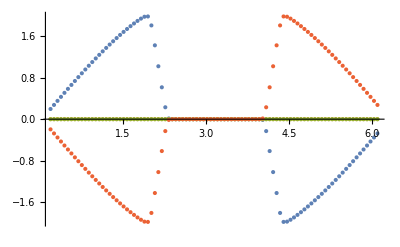

```mathematica
ListPlot[ velocityDispersion[ ed1 ,P]
		, PlotRange->All
	]
```

### Iterative visualization

```mathematica
Manipulate[
ListPlot[ velocityDispersion[ edge[ dispersion[Energies[n,1,κ ,h, P],P,n ],n] ,P]
	,PlotStyle-> { {Black , Thickness[0.006]} 
				,{Black, Thickness[0.006]}  , { Black , Thickness[0.006] } , {Black , Thickness[0.006] }
	                            ,Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7], Hue[1,0,0.5,0.7] ,Hue[1,0,0.5,0.7]
				}
		,FrameLabel->{k , ϵ }  ,
		 FrameTicks->{{0,π/3 , 2π/3  , π, 4π/3 , 5π/3, 2π} , Automatic}   ,Joined->True,PlotStyle->{Black},   Frame->{{True,False} ,{True,False}} , FrameStyle ->Directive[Black,26], FrameTicksStyle->Directive[Black,15],ImageSize->800  ]

	 , {h,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5}, ControlType->Setter}
	 , {κ,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5,}, ControlType->Setter}
	 ,{ {n,15,"dim 'n'"},{5,10,15, 20,30} ,  ControlType->Setter } 
	 ,{ {P,200 , "partitions"},{ 50 , 100,200,300} ,  ControlType->Setter } 
	,ContentSize->Full
]
```

In

## second and third derivative of the energy

### Iterative visualization

second derivative

```mathematica
Manipulate[
ListPlot[ 
		velocityDispersion[ velocityDispersion[ edge[ dispersion[Energies[n,1,κ ,h, P],P,n ],n] ,P] ,P-1]	
		,Joined->True
		
		,PlotStyle-> { {Hue[0,1,0.9,0.5], Thickness[0.005]} 
				,{Hue[0.22,1,0.9,.5], Thickness[0.005]}  , { Hue[0.5,1,0.9,.5] , Thickness[0.005] } , {Hue[0.85,1,0.9,.5] , Thickness[0.005] }	}
		,FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π} , {-2,-1, 0 , 1, 2 }}   , Frame -> {{True,False},{True,False} }  
		,PlotTheme->"Scientific" 
		, PlotRange-> Automatic
	]

	 , {h,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5, 0.75 , 1}, ControlType->Setter}
	 , {κ,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5, 0.75 , 1}, ControlType->Setter}
	 ,{ {n,15,"dim 'n'"},{5,10,15, 20,30} ,  ControlType->Setter } 
	 ,{ {P,300 , "partitions"},{ 300,500,1000} ,  ControlType->Setter } 
	,ContentSize->Full
]
```

Part::partd: Part specification List⟦3⟧ is longer than depth of object.

Part::partd: Part specification List⟦4⟧ is longer than depth of object.

Part::partd: Part specification List⟦5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 296 of {{π/50,-16.3685},{(2 π)/75,-16.3547},{π/30,-16.3374},{π/25,-16.3167},{(7 π)/150,-16.2926},{(4 π)/75,-16.265},{(3 π)/50,-16.234},{π/15,-16.1996},{(11 π)/150,-16.1617},{(2 π)/25,-16.1204},{(13 π)/150,-16.0757},{(7 π)/75,-16.0276},{π/10,-15.9761},{(8 π)/75,-15.9212},{(17 π)/150,-15.8628},«22»,{(4 π)/15,-13.6074},{(41 π)/150,-13.4708},{(7 π)/25,-13.3312},{(43 π)/150,-13.1885},{(22 π)/75,-13.0428},{(3 π)/10,-12.8941},{(23 π)/75,-12.7424},{(47 π)/150,-12.5877},{(8 π)/25,-12.43},{(49 π)/150,-12.2695},{π/3,-12.106},{(17 π)/50,-11.9396},{(26 π)/75,-11.7704},«245»} does not exist.

Part::partw: Part 297 of {{π/50,-16.3685},{(2 π)/75,-16.3547},{π/30,-16.3374},{π/25,-16.3167},{(7 π)/150,-16.2926},{(4 π)/75,-16.265},{(3 π)/50,-16.234},{π/15,-16.1996},{(11 π)/150,-16.1617},{(2 π)/25,-16.1204},{(13 π)/150,-16.0757},{(7 π)/75,-16.0276},{π/10,-15.9761},{(8 π)/75,-15.9212},{(17 π)/150,-15.8628},«22»,{(4 π)/15,-13.6074},{(41 π)/150,-13.4708},{(7 π)/25,-13.3312},{(43 π)/150,-13.1885},{(22 π)/75,-13.0428},{(3 π)/10,-12.8941},{(23 π)/75,-12.7424},{(47 π)/150,-12.5877},{(8 π)/25,-12.43},{(49 π)/150,-12.2695},{π/3,-12.106},{(17 π)/50,-11.9396},{(26 π)/75,-11.7704},«245»} does not exist.

Part::partw: Part 298 of {{π/50,-16.3685},{(2 π)/75,-16.3547},{π/30,-16.3374},{π/25,-16.3167},{(7 π)/150,-16.2926},{(4 π)/75,-16.265},{(3 π)/50,-16.234},{π/15,-16.1996},{(11 π)/150,-16.1617},{(2 π)/25,-16.1204},{(13 π)/150,-16.0757},{(7 π)/75,-16.0276},{π/10,-15.9761},{(8 π)/75,-15.9212},{(17 π)/150,-15.8628},«22»,{(4 π)/15,-13.6074},{(41 π)/150,-13.4708},{(7 π)/25,-13.3312},{(43 π)/150,-13.1885},{(22 π)/75,-13.0428},{(3 π)/10,-12.8941},{(23 π)/75,-12.7424},{(47 π)/150,-12.5877},{(8 π)/25,-12.43},{(49 π)/150,-12.2695},{π/3,-12.106},{(17 π)/50,-11.9396},{(26 π)/75,-11.7704},«245»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

third derivative:

```mathematica
Manipulate[
ListPlot[ 
		velocityDispersion[velocityDispersion[ velocityDispersion[ edge[ dispersion[Energies[n,1,κ ,h, P],P,n ],n] ,P] ,P-1],P-2]	
		,Joined->True
		
		,PlotStyle-> { {Hue[0,1,0.9,0.5], Thickness[0.005]} 
				,{Hue[0.22,1,0.9,.5], Thickness[0.005]}  , { Hue[0.5,1,0.9,.5] , Thickness[0.005] } , {Hue[0.85,1,0.9,.5] , Thickness[0.005] }	}
		,FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π} , {-2,-1, 0 , 1, 2 }}   , Frame -> {{True,False},{True,False} }  
		,PlotTheme->"Scientific" 
		, PlotRange-> Automatic
	]

	 , {h,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5, 0.75 , 1}, ControlType->Setter}
	 , {κ,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5, 0.75 , 1}, ControlType->Setter}
	 ,{ {n,15,"dim 'n'"},{5,10,15, 20,30} ,  ControlType->Setter } 
	 ,{ {P,300 , "partitions"},{ 300,500,1000} ,  ControlType->Setter } 
	,ContentSize->Full
]
```

## Interaction between edges

We will add a term    φ_bc c   and     φ_c b b    for the terms in the edge and see how it perturbs the spectrum.

[ for practical reasons I will use    φ_b→ φ  and φ_c→ ϕ]

### Hamiltonian and parameters definition

Remember that the size L=2n+ 4, 

The interaction will occur at the matrix position :

		{ 1 , L } and { L , 1 }  for     φ_c b b

		{ 2 , L-1 } and { L-1 , 2}  for  φ_bc c

```mathematica
Hint[k_,n_, J_,κ_,h_, φ_, ϕ_] := SparseArray[   {
					{i_,i_} -> If[ 1<i<2n+ 4 , If[OddQ[i],-α[k,κ], α[k,κ]] , 0],

					{i_,j_} /;Abs[i-j]==1->   
												If[                     ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 
															If[j>i, ⅈ γ[h] , - ⅈ γ[h] ], 
															If[EvenQ[Min[i,j]], -(i-j) ⅈ s[k,J] , -(i-j) ⅈ r[J]] ],

					{i_,j_} /;Abs[i-j]==2-> If[ ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 0,  If[OddQ[i],β[k,κ], -β[k,κ]] ],
					{1,2n+ 4}-> 2 ⅈ ϕ,
					{2n+ 4,1}-> -2ⅈ ϕ,
					{2 , 2n+3} -> 2ⅈ φ,
					{2n+3,2} -> -2 ⅈ φ
},					
	{2n+ 4,2n+ 4}					]
```

```mathematica
ClearAll[k,n,J,κ,h ,φ, ϕ]
```

```mathematica
MatrixForm[Hint[k,1,J,κ,h,φ, ϕ]]
```

(0 | -2 ⅈ h | 0 | 0 | 0 | 2 ⅈ ϕ
2 ⅈ h | 4 κ Sin[k] | -4 ⅈ J Cos[k/2] | -4 κ Sin[k/2] | 2 ⅈ φ | 0
0 | 4 ⅈ J Cos[k/2] | -4 κ Sin[k] | 2 ⅈ J | 4 κ Sin[k/2] | 0
0 | -4 κ Sin[k/2] | -2 ⅈ J | 4 κ Sin[k] | -4 ⅈ J Cos[k/2] | 0
0 | -2 ⅈ φ | 4 κ Sin[k/2] | 4 ⅈ J Cos[k/2] | -4 κ Sin[k] | -2 ⅈ h
-2 ⅈ ϕ | 0 | 0 | 0 | 2 ⅈ h | 0)

### Dispersion

```mathematica
interactionDispersion[n_,J_,κ_ ,h_, P_ ,φ_, ϕ_] :=  dispersion[Table[  N@ {   k, Sort[N@Eigenvalues[  N@Hint[k, n, J,κ,h,φ, ϕ] ]]    }     , {k,0,π , π/P}]  , P,n]
```

```mathematica
P=10
```

10

```mathematica
Manipulate[ ListPlot[  Quiet@interactionDispersion[n,1,κ ,h, P ,φ, ϕ]   , 
PlotStyle->  Join[  {{Hue[0,0.51,0.38,0.5], Thickness[0.005]} },
					Table[ {Hue[0,0,0.9,0.5], Thickness[0.005]} , {i,2,n,1}] ,
					{{Hue[0,1,0.7,0.7], Thickness[0.006]} ,
					{Hue[0.26,1,0.86,0.55], Thickness[0.006]}  , 
					{ Hue[0.5,1,0.9,.5] , Thickness[0.006] } , 
					{Hue[0.85,1,0.9,.5] , Thickness[0.006] }},
					Table[ {Hue[0,0,0.9,0.5], Thickness[0.005]} , {I,n+5,2n+3,1}] ,
					{{Hue[1,0.51,0.38,0.5], Thickness[0.005]} }
			]	,
FrameLabel->{k , E }  ,   
Ticks->Automatic ,
Joined-> j, 
FrameTicks->{{0,π/6,π/3,π/2 , 2π/3 , 5π/6 , π} , {-6 ,-4,-2,0 , 2, 4 , 6}}   ,
Frame -> {{True,False},{True,False} },
FrameTicksStyle->Black ]

	 , {h,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5, 0.75 , 1}, ControlType->Setter}
	 , {κ,{ 0,0.05, 0.1, 0.15, 0.20, 0.25,0.5, 0.75 , 1}, ControlType->Setter}
	 ,{ {n,30,"dim 'n'"},{5,10,15, 20,30,50,100} ,  ControlType->Setter } 
	 ,{ {P,200 , "partitions"},{ 50 , 100,200,300} ,  ControlType->Setter } 
	 , {φ,{ 0,0.05, 0.1  , 0.5,1,1.5,2,5,10}  ,  ControlType->Setter}
	 , {ϕ,{0,0.05, 0.1, 0.5,1,2,5}   ,  ControlType->Setter }
	,  { {j,True, "Joined"},{True , False }   ,  ControlType->SetterBar }
	,ContentSize->Full

		]
```